```mathematica
Clear[tubeLaw,hoopPressure]
tubeLaw[r_,r0_,P0_,n_]:=P0(1-(r/r0)^(2/n))
hoopPressure[r_,r0_,τ_,E_,P0_]:=If[r<r0,tubeLaw[r,r0,-P0,(-2 P0 r0)/(E τ)],τ E(r-r0)/(r r0)]
```

```mathematica
Clear[limitPressure,poiseuilleConductance,poiseuilleFlow,curve,flow]
limitPressure[r_,L_,ρ_,μ_,ReLimit_,λ_:1]:=ReLimit 4(μ^2 L)/(r^3 ρ)λ
poiseuilleConductance[r_,L_,μ_,λ_]:=(π r^4)/(8μ L)λ
poiseuilleFlow[dP_,r_,L_,μ_,λ_]:=poiseuilleConductance[r,L,μ,λ]dP
curve[x_,x0_]:=If[x<x0,x,√((2 x-x0) x0)]
flow[dP_,r_,L_,ρ_,μ_,ReLimit_,λ_]:=poiseuilleConductance[r,L,μ,λ]curve[dP,limitPressure[r,L,ρ,μ,ReLimit,λ]]
```

```mathematica
ρWater=1 10^3;
ηWater=1. 10^-3;
```

```mathematica
flow[x[t]-hoopPressure[r,r0,τ,ym,-1000],r0,L,ρWater,ηWater,3000,1]
```

1/L 392.699 r0^4 If[-If[r<r0,tubeLaw[r,r0,-(-1000),-(2 (-1000) r0)/(ym τ)],(τ ym (r-r0))/(r r0)]+x[t]<(0.000012 L)/r0^3,-If[r<r0,tubeLaw[r,r0,-(-1000),-(2 (-1000) r0)/(ym τ)],(τ ym (r-r0))/(r r0)]+x[t],√(((2 (-If[r<r0,tubeLaw[r,r0,-(-1000),-(2 (-1000) r0)/(ym τ)],(τ ym (r-r0))/(r r0)]+x[t])-(0.000012 L)/r0^3) (0.000012 L))/r0^3)]

```mathematica
Clear[P,Q]
P[v_,v0_,k1_]:=k1(v-v0)
Q[dp_,k2_]:=k2 curve[dp,1000]
```

```mathematica
Clear[P,Q]
P[v_]:=hoopPressure[√(v/(π 1.000)),0.010,0.001,1000000,-1000]
Q[dp_]:=flow[dp,0.010,1.000,ρWater,ηWater,3000,1]
P[v]//Simplify
Q[dp]//Simplify
```

Piecewise[{{100000.-1772.45/(√v), 1. √v≥0.0177245}, {1000.-1.38837×10^178 v^50., True}}]

3.92699×10^-6 If[dp<12.,dp,√((2 dp-12.) 12.)]

```mathematica
π 0.010^2 1.000
```

0.000314159

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

{{x→InterpolatingFunction[…],v1→InterpolatingFunction[…],v2→InterpolatingFunction[…]}}

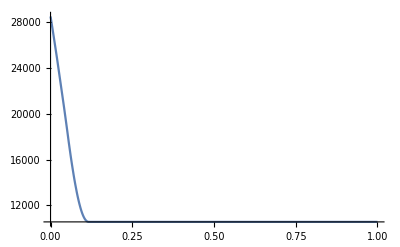

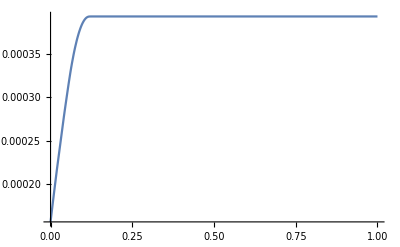

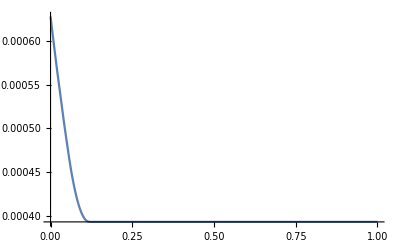

```mathematica
s=With[{v10=0.5 0.0003141592653589793,v20=2 0.0003141592653589793},NDSolve[{
v1'[t]==Q[x[t]-P[v1[t]]],
v2'[t]==Q[x[t]-P[v2[t]]],
v1'[t]+v2'[t]==0,
v1[0]==v10,
v2[0]==v20
},{x,v1,v2},{t,0,1}]]
Plot[Evaluate[x[t]/.s],{t,0,1},PlotRange->All]
Plot[Evaluate[v1[t]/.s],{t,0,1},PlotRange->All]
Plot[Evaluate[v2[t]/.s],{t,0,1},PlotRange->All]
```

```mathematica
Solve[{
q1==Q[x-P[v1,v10,k11],k12],
q2==Q[x-P[v2,v20,k21],k22],
q1+q2==0
},{x,q1,q2}]
```

{{x→-(-k11 k12 v1+k11 k12 v10-k21 k22 v2+k21 k22 v20)/(k12+k22),q1→-(k11 k12 k22 v1-k11 k12 k22 v10-k12 k21 k22 v2+k12 k21 k22 v20)/(k12+k22),q2→-(-k11 k12 k22 v1+k11 k12 k22 v10+k12 k21 k22 v2-k12 k21 k22 v20)/(k12+k22)}}